# Intuitionistic Hilbert curve

## Andrej Bauer – February 1, 2024

We define a generalized Hilbert curve [0,1]→[0,1]^2 parameterized by a scaling factor 0<k<1.

```mathematica
ClearAll[vertices,hilbert]

vertices[k_,1]:=N[{{1/4,1/4},{1/4,3/4},{3/4,3/4},{3/4,1/4}}]
vertices[k_,n_]:=
Module[{s=ScalingTransform[{k,k}][vertices[k,n-1]]},
Join[
ReflectionTransform[{-1,1}][s],
TranslationTransform[{0,1-k}][s],
TranslationTransform[{1-k,1-k}][s],
TranslationTransform[{1-k,0}][ReflectionTransform[{1,1},{k,0}][s]]
]
]

hilbert[k_,n_]:=Graphics[{{Gray,Thin,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}, Line@vertices[k,n]}]
```

When k=1/2 we recover the usual Hilbert curve:

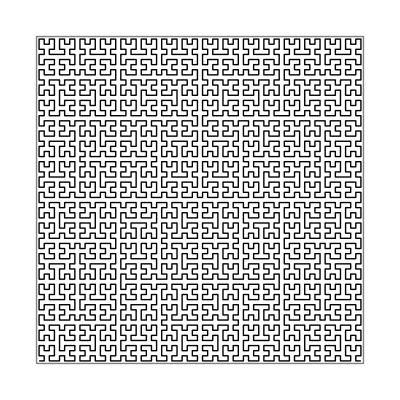

```mathematica
hilbert[1/2,6]
```

With k<1/2 the curve is not space-filling anymore:

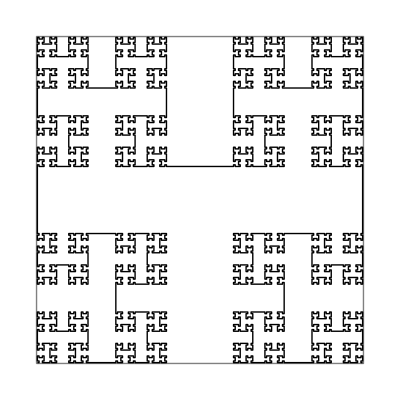

```mathematica
hilbert[2/5,6]
```

With k>1/2 the curve is space-filling constructively (assuming dependent choice):

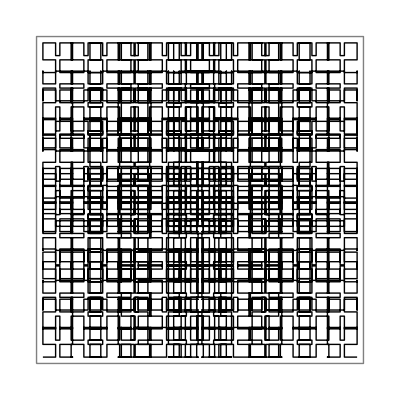

```mathematica
hilbert[3/5,6]
```

It is fun to manipulate k interactively:

```mathematica
Manipulate[hilbert[k,n],{{k,0.5},0,1},{{n,5},1,10,1}]
```

## Creating an animation

```mathematica
ClearAll[animate]
animate[k1_,k2_,n_,f_]:=Do[Export["~/hilbert-"<>ToString[10000+i]<>".png",hilbert[k1+(k2-k1)*i/f,n],ImageSize->{512,512}],{i,0,f}]
```

animate[0.4, 0.8, 8, 300]

This will generate 50 PNG files in your home directory: animate[0.4, 0.6, 6,50]

You may use ffmpeg to convert the generated images to a movie:

ffmpeg -i hilbert-1%04d.png -pix_fmt yuv420p hilbert.mp4